# AMS-511 Foundations of Quantitative Finance

## Fall 2018 — Assignment 05

Robert J. Frey, Research Professor
Stony Brook University, Applied Mathematics and Statistics

Robert.Frey@StonyBrook.edu
http://www.ams.sunysb.edu/~frey

## Question 1

You are given the following annual data on four investments, i∈{1,2,3,4} in a market M:

r_f=0.02

μ_M=0.085

σ_M=0.105

β={0.9,1.2,0.6,2.1}

σ_ϵ={0.05,0.07,0.04,0.09}

Under the assumption that the CAPM applies:

Compute the covariance matrix and correlation matrix of the assets.

```mathematica
nRiskFree=0.02;
nMarketReturn=0.085;
nMarketStdDev = 0.105;
nMarketVar= nMarketStdDev^2;
vnBeta={0.9,1.2,0.6,2.1};
vnErrorStdDev = {0.05,0.07,0.04,0.09};
vnErrorVar=vnErrorStdDev^2;

vnExpectedReturn=(nMarketReturn-nRiskFree)vnBeta+nRiskFree
mnCovariance=nMarketVar Outer[Times,vnBeta,vnBeta]+DiagonalMatrix[vnErrorVar]
mnInvStdDev=Inverse[Sqrt[DiagonalMatrix[Diagonal[mnCovariance]]]];
mnCorrelation=mnInvStdDev*mnCovariance*mnInvStdDev;
```

{0.0785,0.098,0.059,0.1565}

{{0.0114303,0.011907,0.0059535,0.0208372},{0.011907,0.020776,0.007938,0.027783},{0.0059535,0.007938,0.005569,0.0138915},{0.0208372,0.027783,0.0138915,0.0567203}}

Compute the mean-variance efficient portfolio such that 𝟙^T x=1.

```mathematica
vnPositions=#/Total[#]&[Inverse[mnCovariance].(vnExpectedReturn-nRiskFree)]
```

{0.29052,0.197633,0.302625,0.209222}

Compute the mean and standard deviation of that portfolio.

```mathematica
xPortSdevMean[x_,{μ_,Σ_}]:={√(x.Σ.x),μ.x};
xPortSdevMean[vnPositions,{vnExpectedReturn, mnCovariance}]
```

{0.121337,0.092772}

The investor wishes to keep 10% of its assets in cash and place the remainder in the optimal portfolio. Assuming returns are Normally distributed

What is the mean and standard deviation of return for the combined cash-risky portfolio?

```mathematica
0.1nRiskFree+0.9nMarketReturn
0.9nMarketStdDev
```

0.0785

0.0945

What is the largest loss one would expect in a given year at a 1% confidence level?

```mathematica
nVaR=InverseCDF[NormalDistribution[0.1nRiskFree+0.9nMarketReturn,0.9nMarketStdDev],1-0.99]
```

-0.14134

The investor wants to see a plot of the percentage held in cash from 5% to 25% against the largest expected loss at a 1% level.

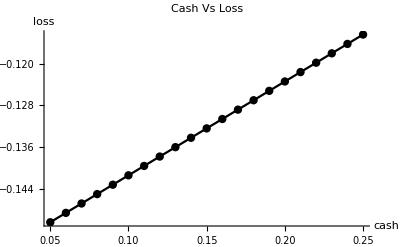

```mathematica
mnCashVsLoss=Table[
{
cash,
InverseCDF[NormalDistribution[cash nRiskFree+(1-cash)nMarketReturn,(1-cash)nMarketStdDev],1-0.99]
},
{cash,0.05,0.25,0.01}
];
ListPlot[
mnCashVsLoss,
PlotStyle->{PointSize[Large],Black},
PlotLabel->Style["Cash Vs Loss",FontSize->14],
Joined->True,Mesh->All,
AxesLabel->{"cash","loss"}
]
```